```mathematica
csvPath = "M:\\JI Courses\\Sophomore_Year\\2019_Spring\\VE401\\Proj2\\Figures\\2\\data.csv";
SystemOpen@csvPath
Data = Import[csvPath];
PosDate = Position[Data,"2019-01-01"];
AllDate = Data[[2;;PosDate[[1,1]]-1,PosDate[[1,2]];;PosDate[[1,2]]]];
For[i=1,i<=Length[AllDate],i++,AllDate[[i]]=DateObject[StringCases[AllDate[[i,1]],x:DatePattern[{"Year","Month","Day"}]:>DateList[x]][[1;;1,1;;3]]]];
Count1 = Tally[AllDate];
Count2 = Tally[Count1[[All,2]]]
```

{{2,324},{1,287},{3,310},{4,227},{6,53},{5,116},{7,21},{8,11},{9,3},{10,1}}

```mathematica
(*Occurence of number of shoot in a day*)
n=365+366+365+365;
NumZero = n;
For[i=1,i≤10,i++,NumZero = NumZero-Count2[[i,2]]];
Insert[Count2,{0,NumZero},1]
```

{{0,108},{2,324},{1,287},{3,310},{4,227},{6,53},{5,116},{7,21},{8,11},{9,3},{10,1}}

```mathematica
(*The fit done by Mathematica*)
Needs["HypothesisTesting`"];
TestData = Join[Table[0,{i,1,108}],Table[1,{i,1,287}],Table[2,{i,1,324}],Table[3,{i,1,310}],Table[4,{i,1,227}],Table[5,{i,1,116}],Table[6,{i,1,53}],Table[7,{i,1,21}],Table[8,{i,1,11}],Table[9,{i,1,3}],Table[10,{i,1,1}]];
PearsonChiSquareTest[TestData,PoissonDistribution[k1],{"FittedDistributionParameters","DegreesOfFreedom","TestDataTable"}]
```

{{k1→2.69884},6, | Statistic | P-Value
Pearson χ^2 | 8.06532 | 0.233357}

```mathematica
(*The fit done considering Pearson Criteria 3.1.2*)
```

```mathematica
Count2= {{0,108},{1,287},{2,324},{3,310},{4,227},{5,116},{6,53},{7,21},{8,11},{9,3},{10,1}};
k2 = 0;
For[i=1,i≤11,i++,k2 = k2+Count2[[i,1]]*Count2[[i,2]]];
k2 = N[k2/n]
```

2.69884

```mathematica
e= N[Exp[1]];
CRV={};
For[i=0,i≤10,i++,CRV =Insert[CRV,e^(-k2)*k2^i/Factorial[i],-1]];
CRV[[11]]=1;
For[i=1,i≤10,i++,CRV[[11]] = CRV[[11]]-CRV[[i]]];
CRV
```

{0.0672838,0.181588,0.245038,0.220439,0.148732,0.0802808,0.0361108,0.0139224,0.0046968,0.00140843,0.000499723}

```mathematica
ExpectedE = {};
For[i=0,i≤10,i++,ExpectedE =Insert[ExpectedE,n*CRV[[i+1]],-1]];
ExpectedE
```

{98.3016,265.3,358.,322.062,217.298,117.29,52.7579,20.3407,6.86203,2.05772,0.730095}

```mathematica
(*We see that the Pearson Criteria 3.1.2 is not satisfied, therefore we merge the last 2 categories and obtain the following*)
Count3 = {{0,108},{1,287},{2,324},{3,310},{4,227},{5,116},{6,53},{7,21},{8,11},{9,4}};
NewCRV={0.06728375768633715,0.18158785527530966,0.24503795802551198,0.220439121262741,0.1487322818512984,0.08028081962213136,0.03611079988250787,0.01392244880578161,0.004696801475119516,0.0014084332052928933+0.000499722907968528};
NewExpectedE={98.30156997973859,265.29985655722743,358.000456675273,322.0615561648646,217.29786378474694,117.29027746793392,52.757878628344,20.34069770524693,6.862026955149613,2.057720912932917+0.7300951685420194};
NewObservedE= {108,287,324,310,227,116,53,21,11,3+1};
(*The Degree of Fredom is found by*)
DegreesOfFreedom = Length[NewExpectedE]-1-1
```

8

```mathematica
(*The Pearson Statistic is found by*)
Stat = 0;
For[i=1,i≤10,i++,Stat=Stat+(NewObservedE[[i]]-NewExpectedE[[i]])^2/NewExpectedE[[i]]];
Stat
```

9.9049

```mathematica
(*Fix alpha=0.05, we test the null hypothesis, and fail to reject it*)
```

```mathematica
Solve[CDF[ChiSquareDistribution[DegreesOfFreedom],x]==0.95,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→15.5073}}

```mathematica
(*The P value is found by:*)
```

```mathematica
PValue = 1-CDF[ChiSquareDistribution[DegreesOfFreedom],Stat]
```

0.271764

```mathematica
(*The Histograms are created as*)
```

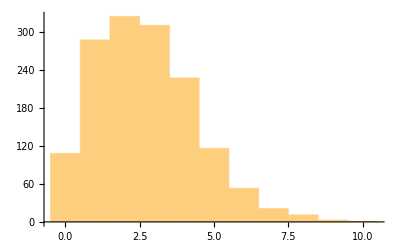

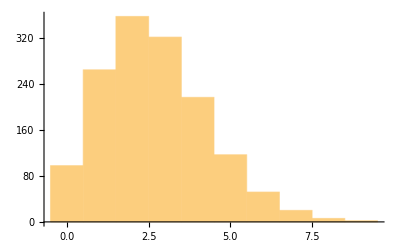

```mathematica
ExpectedData = Join[
Table[0,{i,1,98.30156997973859}],Table[1,{i,1,265.29985655722743}],Table[2,{i,1,358.000456675273}],Table[3,{i,1,322.0615561648646}],Table[4,{i,1,217.29786378474694}],Table[5,{i,1,117.29027746793392}],Table[6,{i,1,52.757878628344}],
Table[7,{i,1,20.34069770524693}],Table[8,{i,1,6.862026955149613}],Table[9,{i,1,2.057720912932917}],
Table[10,{i,1,0.7300951685420194}]];
Histogram[TestData]
Histogram[ExpectedData]
```

```mathematica
(*The BarCharts are created as*)
```

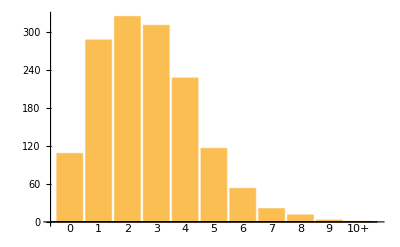

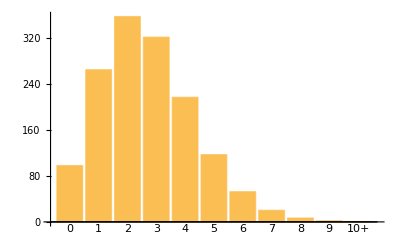

```mathematica
BarO= {108,287,324,310,227,116,53,21,11,3,1};
BarE= ExpectedE;
BarChart[BarO,ChartLabels->{"0","1","2","3","4","5","6","7","8","9","10+"}]
BarChart[BarE,ChartLabels->{"0","1","2","3","4","5","6","7","8","9","10+"}]
```